```mathematica
AoA=Table[a,{a,-0.4,0.39,0.01}]
```

{-0.4,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.3,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39}

```mathematica
DecimalForm[AoA,{2,2}]
```

{-0.40,-0.39,-0.38,-0.37,-0.36,-0.35,-0.34,-0.33,-0.32,-0.31,-0.30,-0.29,-0.28,-0.27,-0.26,-0.25,-0.24,-0.23,-0.22,-0.21,-0.20,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.10,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.00,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.10,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.20,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.30,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39}

```mathematica
forceOverAoA=Map[Import["/home/tatjam/code/tfg/workdir/clalpha/aero_force_2d_" <> ToString[DecimalForm[#,{2,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
pair[a_,b_]:={b,a[[2]]}
```

```mathematica
MapThread[pair,{forceOverAoA,AoA}];
```

```mathematica
model=LinearModelFit[MapThread[pair,{forceOverAoA,AoA}],x,x]
```

FittedModel[0.000964343+4.78979 x]

```mathematica
model["BestFitParameters"][[2]]
```

4.78979

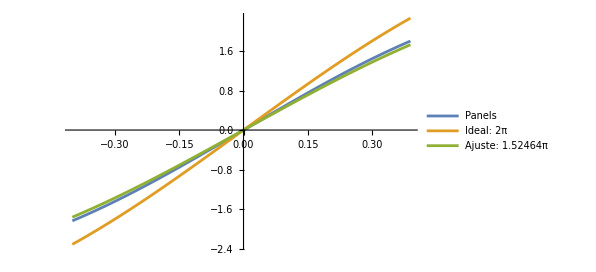

```mathematica
ListLinePlot[{MapThread[pair,{forceOverAoA,AoA}],Map[{#1,2π*#1*Cos[#1]}&,AoA],Map[{#1,model["BestFitParameters"][[2]]*#1*Cos[#1]}&,AoA]},
PlotLegends->{"Panels", "Ideal: 2π","Ajuste: "<>ToString[(model["BestFitParameters"][[2]])/π]<>"π"}]
```